#### License & copyright

MIT License

Copyright (c) 2016 Johanna Erdmenger, Daniel Fernandez, Priesley Goulart and Piotr Witkowski

Permission is hereby granted, free of charge, to any person obtaining a copy
of this software and associated documentation files (the “Software”), to deal
in the Software without restriction, including without limitation the rights
to use, copy, modify, merge, publish, distribute, sublicense, and/or sell
copies of the Software, and to permit persons to whom the Software is
furnished to do so, subject to the following conditions:

The above copyright notice and this permission notice shall be included in all
copies or substantial portions of the Software.

THE SOFTWARE IS PROVIDED “AS IS”, WITHOUT WARRANTY OF ANY KIND, EXPRESS OR
IMPLIED, INCLUDING BUT NOT LIMITED TO THE WARRANTIES OF MERCHANTABILITY,
FITNESS FOR A PARTICULAR PURPOSE AND NONINFRINGEMENT. IN NO EVENT SHALL THE
AUTHORS OR COPYRIGHT HOLDERS BE LIABLE FOR ANY CLAIM, DAMAGES OR OTHER
LIABILITY, WHETHER IN AN ACTION OF CONTRACT, TORT OR OTHERWISE, ARISING FROM,
OUT OF OR IN CONNECTION WITH THE SOFTWARE OR THE USE OR OTHER DEALINGS IN THE
SOFTWARE.

## Numerics for section 5.2

### GR Definitions

```mathematica
(*METRIC DEFINITION*)

metric[lineelement_,independentvars_List]:=Block[{lenindependent,differentials,diffmatrix,metricform,varmetric,gh,sum,equation,rule,varhelp,zeros,zerorule},(*---determine the number of independent variables---*)lenindependent=Length[independentvars];
(*---create the differentials corresponding to dx,dt....---*)differentials=Map[Dt,independentvars];
(*---a matrix of differential products---*)diffmatrix=Outer[Times,differentials,differentials];
(*---the general metric form---*)metricform=Array[gh,{lenindependent,lenindependent}];
varmetric=Variables[metricform];
(*---built a system of equations to determine the elements of the metric---*)If[Length[metricform]==Length[diffmatrix],sum=0;
Do[Do[sum=sum+metricform[[i,j]] diffmatrix[[i,j]],{j,1,lenindependent}],{i,1,lenindependent}],sum=0];
(*---construct the metric tensor---*)If[sum===0,Return[sum],sum=sum-lineelement;
equation=CoefficientList[sum,differentials]==0;
rule=Solve[equation,varmetric];
metricform=metricform/.rule;
varmetric=Variables[metricform];
(*---replace the nonzero elements---*)varhelp={};
Do[If[Not[FreeQ[varmetric[[i]],gh]],AppendTo[varhelp,varmetric[[i]]]],{i,1,Length[varmetric]}];
zeros=Table[0,{Length[varhelp]}];
SubstRule[x_,y_]:=x->y;
zerorule=Thread[SubstRule[varhelp,zeros]];
metricform=Flatten[metricform/.zerorule,1];
(*---make the metricform symmetric---*)metricform=Expand[(metricform+Transpose[metricform])/2]];
metricform];
Off[Solve::svars];
```

```mathematica
(*CHRISTOFFELSYMBOLS*)
Christoffel[m_,a_,b_,g_,ginv_]:=Block[{n},Expand[Sum[ginv[[m,n]] (D[g[[a,n]],IndepVar[[b]]]+D[g[[b,n]],IndepVar[[a]]]-D[g[[a,b]],IndepVar[[n]]]),{n,1,Length[g]}]/2]]
```

```mathematica
(*RIEMANNTENSOR Subscript[R^a, bcd]*)
Riemann[a_,b_,c_,d_,g_,ing_]:=Block[{},Expand[D[Christoffel[a,b,d,g,ing],IndepVar[[c]]]-D[Christoffel[a,b,c,g,ing],IndepVar[[d]]]+Sum[Christoffel[e,b,d,g,ing] Christoffel[a,e,c,g,ing],{e,1,Length[g]}]-Sum[Christoffel[e,b,c,g,ing] Christoffel[a,e,d,g,ing],{e,1,Length[g]}]]]
(*Riemanntensor Subscript[R, rstu]*)
Rie[r_,s_,t_,u_,g_,ginv_]:=Sum[g[[r,j]] Riemann[j,s,t,u,g,ginv],{j,1,Length[g]}]
```

```mathematica
(**RICCITENSOR Subscript[Ric, ab]*)
Ricci[m_,q_,g_,ing_]:=Block[{a},Expand[Sum[Riemann[a,m,a,q,g,ing],{a,1,Length[g]}]]]
```

```mathematica
(*RICCISCALAR R*)
RicciScalar[g_,ing_]:=Block[{},Expand[Sum[ing[[a,b]] Ricci[a,b,g,ing],{a,1,Length[g]},{b,1,Length[g]}]]];
```

```mathematica
(*EINSTEINFIELDTENSOR G_ab*)
Einstein[m_,n_,g_,ing_]:=Ricci[m,n,g,ing]-(RicciScalar[g,ing] g[[m,n]])/2
```

### Equations of Motion

#### Derivation

The ansatz for the metric. In principle, we are free to select 3 functions. But then we end up with more unknowns than equations.
That’s because of the gauge freedom of redefining the radial coordinate r → R[r], so what we can do is fix the g_xx, g_yy components by choosing

```mathematica
g[r_]:=(1-(1-r)^2)/rp;
```

Now f[r] corresponds to the usual blackening factor and G[r] multiplies the (r,t) part. Those are the free metric functions.

```mathematica
IndepVar = {t,r,x,y};dim=Length[IndepVar];
mybg=({{-(f[r]G[r])/g[r]^2, 0, 0, 0}, {0, (g'[r]^2 G[r])/(g[r]^2 f[r]), 0, 0}, {0, 0, 1/g[r]^2, 0}, {0, 0, 0, 1/g[r]^2}});
invbg=Inverse[mybg]//FullSimplify;
```

Ansatz for the gauge field: constant magnetic field, and an A_t component for electric field.

```mathematica
A={At[r],0,-B/2 y,B/2 x};
F=({{0, -At'[r], 0, 0}, {At'[r], 0, 0, 0}, {0, 0, 0, B}, {0, 0, -B, 0}});
```

EOM:

```mathematica
eq1=Table[Ricci[a,b,mybg,invbg]-1/2 D[ϕ[r],IndepVar⟦a⟧]D[ϕ[r],IndepVar⟦b⟧]-1/2 V[ϕ[r]]mybg⟦a,b⟧+1/2 Z[ϕ[r]](1/4 mybg⟦a,b⟧Sum[invbg⟦l,m⟧invbg⟦ρ,p⟧F⟦l,ρ⟧F⟦m,p⟧,{l,dim},{ρ,dim},{m,dim},{p,dim}]-Sum[invbg⟦ρ,p⟧F⟦a,ρ⟧F⟦b,p⟧,{ρ,dim},{p,dim}]),{a,dim},{b,dim}]//Simplify;
eq2=Table[Sum[D[Z[ϕ[r]]invbg⟦a,c⟧invbg⟦b,d⟧F⟦c,d⟧,IndepVar⟦a⟧],{a,dim},{c,dim},{d,dim}]+Sum[Christoffel[a,a,ρ,mybg,invbg]Z[ϕ[r]]invbg⟦ρ,p⟧invbg⟦b,c⟧F⟦p,c⟧,{a,dim},{ρ,dim},{p,dim},{c,dim}]+Sum[Christoffel[b,a,ρ,mybg,invbg]Z[ϕ[r]]invbg⟦a,c⟧invbg⟦ρ,p⟧F⟦c,p⟧,{a,dim},{ρ,dim},{p,dim},{c,dim}],{b,dim}]//Simplify;
eq3=Sum[invbg⟦a,b⟧D[ϕ[r],IndepVar⟦a⟧,IndepVar⟦b⟧],{a,dim},{b,dim}]-Sum[invbg⟦a,b⟧Christoffel[ρ,b,a,mybg,invbg]D[ϕ[r],IndepVar⟦ρ⟧],{a,dim},{b,dim},{ρ,dim}]-V'[ϕ[r]]-1/4 Z'[ϕ[r]]Sum[invbg⟦l,m⟧invbg⟦ρ,p⟧F⟦l,ρ⟧F⟦m,p⟧,{l,dim},{ρ,dim},{m,dim},{p,dim}];
```

```mathematica
eqs=Union[Flatten[Join[eq1,eq2,{eq3}]]][[2;;-1]];
```

Choice of the potentials. If δp and γp are big enough, and γ and δ are negative, they reduce to the choice in subsection 5.2
So this choice connects with that near-boundary behavior for large dilaton at the horizon.

```mathematica
potentialschoice={V->Function[x,4β Cosh[-δ x]],Z->Function[x,1/2 Sech[-γ x]]};
```

#### Choices

There are some free parameters in the couplings, that should be well approximated by exponentials.
Here one can play with different values of γ, δ and AA=B/Q to check agreement between the cosh, sinh expressions and their corresponding exponentials.

```mathematica
Clear[γ,δ,B,Q]
```

```mathematica
trial={γ->-2.2,δ->-2.15,AA->1/40};
```

```mathematica
Cosh[-δ 1/(2γ)Log[AA(γ-δ)/(γ+δ)]]/.trial
1/2 Exp[-δ 1/(2γ)Log[AA(γ-δ)/(γ+δ)]]/.trial
```

26.8946

26.8853

```mathematica
Sech[-γ 1/(2γ)Log[AA(γ-δ)/(γ+δ)]]/.trial
2Exp[γ 1/(2γ)Log[AA(γ-δ)/(γ+δ)]]/.trial
```

0.0338934

0.0339032

```mathematica
Clear[γ,δ,B,Q]
```

#### Equations to Solve

Let’s look now at our 5 differential equations.

```mathematica
eqs//Simplify
```

{-((48 (-1+r)^2 rp^4 f[r] G[r]+4 (-1+r)^2 G[r]^2 (2 rp^4 V[ϕ[r]]+B^2 (-2+r)^4 r^4 Z[ϕ[r]])+(-2+r)^4 r^4 rp^2 Z[ϕ[r]] At'[r]^2-8 r (2-3 r+r^2) rp^4 G[r] f'[r])/(16 (-2+r)^2 (-1+r)^2 r^2 rp^2 G[r]^2)),1/(4 (-1+r)^3 rp^2 G[r]^3)(-2+r)^4 r^4 ((-1+r) Z[ϕ[r]] At'[r] G'[r]+G[r] (-(-1+r) At'[r] Z'[ϕ[r]] ϕ'[r]+Z[ϕ[r]] (At'[r]-(-1+r) At''[r]))),(f[r] (G[r] (-4 (-1+r)^3 G[r]^2 (-2 rp^4 V[ϕ[r]]+B^2 (-2+r)^4 r^4 Z[ϕ[r]])-(-2+r)^2 (-1+r) r^2 rp^2 ((-2+r)^2 r^2 Z[ϕ[r]] At'[r]^2-2 rp^2 f'[r] G'[r])+2 (-2+r) r rp^4 G[r] ((-8+18 r-9 r^2) f'[r]+r (2-3 r+r^2) f''[r]))+2 rp^4 f[r] (24 (-1+r)^3 G[r]^2-(-2+r)^2 (-1+r) r^2 G'[r]^2+(-2+r) r G[r] ((-4+10 r-5 r^2) G'[r]+r (2-3 r+r^2) G''[r]))))/(16 (-2+r)^2 (-1+r)^3 r^2 rp^2 G[r]^2),(G[r] (4 (-1+r)^3 G[r]^2 (-2 rp^4 V[ϕ[r]]+B^2 (-2+r)^4 r^4 Z[ϕ[r]])+(-2+r)^2 (-1+r) r^2 rp^2 ((-2+r)^2 r^2 Z[ϕ[r]] At'[r]^2-2 rp^2 f'[r] G'[r])-2 (-2+r) r rp^4 G[r] ((-8+18 r-9 r^2) f'[r]+r (2-3 r+r^2) f''[r]))-2 rp^4 f[r] (-(-2+r)^2 (-1+r) r^2 G'[r]^2+(-1+r) G[r]^2 (24 (-1+r)^2+(-2+r)^2 r^2 ϕ'[r]^2)+(-2+r) r G[r] ((4-6 r+3 r^2) G'[r]+r (2-3 r+r^2) G''[r])))/(4 (-2+r)^2 (-1+r) r^2 rp^4 f[r] G[r]^2),1/(8 (-1+r)^3 rp^4 G[r]^2)((-2+r)^4 (-1+r) r^4 rp^2 At'[r]^2 Z'[ϕ[r]]-4 (-1+r)^3 G[r]^2 (2 rp^4 V'[ϕ[r]]+B^2 (-2+r)^4 r^4 Z'[ϕ[r]])+2 (-2+r) r rp^4 G[r] (r (2-3 r+r^2) f'[r] ϕ'[r]+f[r] ((-4+10 r-5 r^2) ϕ'[r]+r (2-3 r+r^2) ϕ''[r])))}

First we need to normalize the functions so that they go to finite values at the horizon.

```mathematica
eqsn=eqs/.{f->Function[r,fn[r](r-1)^4],At->Function[r,Atn[r](r-1)^2]}//Simplify;
```

We can solve for 3 second derivatives:

```mathematica
repl1=Solve[{eqsn⟦2⟧==0,eqsn⟦4⟧==0,eqsn⟦5⟧==0},{ϕ''[r],Atn''[r],fn''[r]}]⟦1⟧//Simplify
```

{ϕ''[r]→1/(2 r^2 (2-3 r+r^2)^2 fn[r])G[r] (-((-2+r)^4 r^4 (2 Atn[r]+(-1+r) Atn'[r])^2 Z'[ϕ[r]])/(rp^2 G[r]^2)+(4 (2 rp^4 V'[ϕ[r]]+B^2 (-2+r)^4 r^4 Z'[ϕ[r]]))/rp^4+(2 r (2-3 r+r^2) (4-2 r+r^2) fn[r] ϕ'[r])/G[r]-(2 r^2 (2-3 r+r^2)^2 fn'[r] ϕ'[r])/G[r]),Atn''[r]→1/((-1+r) G[r] Z[ϕ[r]])(Z[ϕ[r]] (2 Atn[r]+(-1+r) Atn'[r]) G'[r]-G[r] (3 Z[ϕ[r]] Atn'[r]+(2 Atn[r]+(-1+r) Atn'[r]) Z'[ϕ[r]] ϕ'[r])),fn''[r]→1/(2 (-1+r)^2 (2-3 r+r^2))(-2+r) fn[r] ((16 (-4+10 r-9 r^2+3 r^3))/((-2+r) r)+(4 (-1+r) G[r] (-2 rp^4 V[ϕ[r]]+B^2 (-2+r)^4 r^4 Z[ϕ[r]]))/((-2+r)^2 r^2 rp^4 fn[r])+(2 (-1+r)^2 (8-2 r+r^2) fn'[r])/((-2+r) r fn[r])+1/(rp^2 fn[r] G[r])(-1+r) ((-2+r)^2 r^2 Z[ϕ[r]] (2 Atn[r]+(-1+r) Atn'[r])^2-2 (-1+r) rp^2 (4 fn[r]+(-1+r) fn'[r]) G'[r])-1/((-2+r)^2 r^2 G[r]^2)2 (-1+r)^2 (-(-2+r)^2 (-1+r) r^2 G'[r]^2+(-1+r) G[r]^2 (24 (-1+r)^2+(-2+r)^2 r^2 ϕ'[r]^2)+(-2+r) r G[r] ((4-6 r+3 r^2) G'[r]+r (2-3 r+r^2) G''[r])))}

And this is what’s left:

```mathematica
eqs2=eqsn/.repl1//Simplify
```

{-1/(16 (-2+r)^2 r^2 rp^2 G[r]^2)(48 (-1+r)^4 rp^4 fn[r] G[r]+4 G[r]^2 (2 rp^4 V[ϕ[r]]+B^2 (-2+r)^4 r^4 Z[ϕ[r]])+(-2+r)^4 r^4 rp^2 Z[ϕ[r]] (2 Atn[r]+(-1+r) Atn'[r])^2-8 (-1+r) r (2-3 r+r^2) rp^4 G[r] (4 fn[r]+(-1+r) fn'[r])),0,-((-1+r)^6 rp^2 fn[r]^2 (8 (-1+r) G'[r]+(-2+r) r G[r] ϕ'[r]^2))/(8 (-2+r) r G[r]),0,0}

Let’s look at the simplest one and solve for a first derivative:

```mathematica
repl2=Solve[eqs2⟦3⟧==0,G'[r]]⟦1⟧
repl2d=D[repl2,r]/.repl2//.repl1//Simplify;
```

{G'[r]→-((-2+r) r G[r] ϕ'[r]^2)/(8 (-1+r))}

With this new info, the original solution is complemented, and we get a final set of equations:

```mathematica
repl1b=repl1/.repl2d/.repl2//Simplify;
repl=Join[repl1b,repl2,repl2d]//Expand//Simplify
```

{ϕ''[r]→-(((-2+r)^4 r^4 rp^2 (2 Atn[r]+(-1+r) Atn'[r])^2 Z'[ϕ[r]]-4 G[r]^2 (2 rp^4 V'[ϕ[r]]+B^2 (-2+r)^4 r^4 Z'[ϕ[r]])+2 r (2-3 r+r^2) rp^4 G[r] (-(4-2 r+r^2) fn[r]+r (2-3 r+r^2) fn'[r]) ϕ'[r])/(2 (-2+r)^2 (-1+r)^2 r^2 rp^4 fn[r] G[r])),Atn''[r]→-1/(8 (-1+r)^2 Z[ϕ[r]])(8 (-1+r) (2 Atn[r]+(-1+r) Atn'[r]) Z'[ϕ[r]] ϕ'[r]+Z[ϕ[r]] (2 (-2+r) r Atn[r] ϕ'[r]^2+(-1+r) Atn'[r] (24+(-2+r) r ϕ'[r]^2))),fn''[r]→((-2+r)^4 r^4 rp^2 (2 Atn[r]+(-1+r) Atn'[r])^2 (4 (-1+r) Z[ϕ[r]]-(-2+r) r Z'[ϕ[r]] ϕ'[r])-(-2+r) (-1+r)^2 r rp^4 G[r] fn'[r] (-8 (8-2 r+r^2)+(-2+r)^2 r^2 ϕ'[r]^2)+2 (-1+r) rp^4 fn[r] G[r] (-32 (3-4 r+2 r^2)+(-2+r)^2 r^2 (3-2 r+r^2) ϕ'[r]^2)-4 G[r]^2 (8 (-1+r) rp^4 V[ϕ[r]]-(-2+r) r (4 B^2 (-2+r)^3 (-1+r) r^3 Z[ϕ[r]]+(2 rp^4 V'[ϕ[r]]+B^2 (-2+r)^4 r^4 Z'[ϕ[r]]) ϕ'[r])))/(8 (-2+r)^2 (-1+r)^3 r^2 rp^4 G[r]),G'[r]→-((-2+r) r G[r] ϕ'[r]^2)/(8 (-1+r)),G''[r]→(ϕ'[r] (8 (-2+r)^4 r^4 rp^2 (2 Atn[r]+(-1+r) Atn'[r])^2 Z'[ϕ[r]]-32 G[r]^2 (2 rp^4 V'[ϕ[r]]+B^2 (-2+r)^4 r^4 Z'[ϕ[r]])+r (2-3 r+r^2) rp^4 G[r] ϕ'[r] (16 r (2-3 r+r^2) fn'[r]+fn[r] (-8 (10-6 r+3 r^2)+(-2+r)^2 r^2 ϕ'[r]^2))))/(64 (-2+r) (-1+r)^3 r rp^4 fn[r])}

What’s left is a constraint. If it is solved at one point, it’ll be solved throughout the bulk.

```mathematica
constr=eqsn/.repl//Simplify
```

{-1/(16 (-2+r)^2 r^2 rp^2 G[r]^2)(48 (-1+r)^4 rp^4 fn[r] G[r]+4 G[r]^2 (2 rp^4 V[ϕ[r]]+B^2 (-2+r)^4 r^4 Z[ϕ[r]])+(-2+r)^4 r^4 rp^2 Z[ϕ[r]] (2 Atn[r]+(-1+r) Atn'[r])^2-8 (-1+r) r (2-3 r+r^2) rp^4 G[r] (4 fn[r]+(-1+r) fn'[r])),0,0,0,0}

```mathematica
replf=Solve[constr⟦1⟧==0,fn'[r]][[1]];
D[constr,r]/.repl/.replf//Simplify
```

{0,0,0,0,0}

### γ = -1, δ = -1 case

This is the choice of coefficients for this section.
ϵ is just there to improve performance.

```mathematica
ϵ=1/1000000;γ0=-(1+ϵ);δ0=-(1-ϵ);B0=1;Q0=1;β0=-3/2;
```

```mathematica
prec=120;
```

#### Bdry conditions

```mathematica
Clear[γ,δ,B,Q,rp]
```

Here we check the result obtained from the attractor equations, and find the BC that we need to impose to our ansatz.
Notice that for the extremal case, the expansion of f[r] starts at the 4th power, like it happened in the RN solution.

```mathematica
fh[r_]:=cf(r-1)^4+O[r,1]^6;Gh[r_]:=cg+O[r,1]^2;Ath[r_]:=ca(r-1)^2+O[r,1]^4;ϕh[r_]:=cϕ+O[r,1]^2;
subs={f->Function[r,fh[r]],G->Function[r,Gh[r]],At->Function[r,Ath[r]],ϕ->Function[r,ϕh[r]]};
```

```mathematica
AdS2xR2cond={cf cg rp^2-cg/cf};
```

We have solutions for v and w. Let’s see if they match what we get from plugging in that expansion into our EOM.

```mathematica
eqsexp0=eqs/.potentialschoice/.subs//FullSimplify
```

{(-2 rp^2 β Cosh[cϕ δ]-((B^2 cg^2+ca^2 rp^2) Sech[cϕ γ])/(8 cg^2 rp^2))+O[r-1]^2,O[r-1]^0,(cf rp^2 (cf+2 cg β Cosh[cϕ δ])-(cf (B^2 cg^2+ca^2 rp^2) Sech[cϕ γ])/(8 cg rp^2)) (r-1)^4+O[r-1]^6,(-8-(16 cg β Cosh[cϕ δ])/cf+((B^2 cg^2+ca^2 rp^2) Sech[cϕ γ])/(cf cg rp^4))/(2 (r-1)^2)+O[r-1]^0,(-4 β δ Sinh[cϕ δ]+((B^2-(ca^2 rp^2)/cg^2) γ Sech[cϕ γ] Tanh[cϕ γ])/(4 rp^4))+O[r-1]^2}

Replacing Cosh, Sinh... by the appropriate exponentials (for large cϕ), and adding an extra condition for having AdS2 x R2 in the IR...

```mathematica
sol0a=FullSimplify[Solve[Join[Normal[eqsexp0],AdS2xR2cond]==0,{ca,cf,cg,B}]]⟦1⟧
```

{ca→-(Sech[cϕ δ] √(-δ Sinh[cϕ δ]-γ Cosh[cϕ δ] Tanh[cϕ γ]))/(√2 √β √γ √Sech[cϕ γ] √Tanh[cϕ γ]),cf→1/rp,cg→-Sech[cϕ δ]/(4 rp β),B→-(2 √2 √(rp^4 β (δ Sinh[cϕ δ]-γ Cosh[cϕ δ] Tanh[cϕ γ])))/(√γ √Sech[cϕ γ] √Tanh[cϕ γ])}

```mathematica
γ=γ0;δ=δ0;B=B0;Q=Q0;β=β0;
rp=((γ B^2)/(2 β(δ-γ)))^(1/4)((Q^2 (γ-δ))/(B^2 (γ+δ)))^((δ+γ)/(8 γ));
```

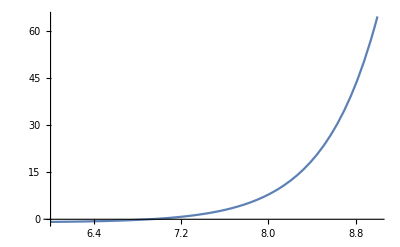

```mathematica
Plot[γ B^2-8 rp^4 β Cosh[cϕ γ] (-γ Cosh[cϕ δ]+δ Coth[cϕ γ] Sinh[cϕ δ]),{cϕ,6,9}]
```

```mathematica
sol0ϕ=FindRoot[γ B^2-8 rp^4 β Cosh[cϕ γ] (-γ Cosh[cϕ δ]+δ Coth[cϕ γ] Sinh[cϕ δ]),{cϕ,8},WorkingPrecision->prec];
sol0=N[Join[sol0a⟦1;;3⟧/.sol0ϕ,sol0ϕ],prec];
```

```mathematica
fh[r_]:=cf(r-1)^4+cf1(r-1)^6+O[r,1]^8;Gh[r_]:=cg+cg1(r-1)^2+O[r, 1]^4;Ath[r_]:=ca(r-1)^2+ca1(r-1)^4+O[r, 1]^6;ϕh[r_]:=cϕ+cϕ1(r-1)^2+O[r, 1]^4;
subs={f->Function[r,fh[r]],G->Function[r,Gh[r]],At->Function[r,Ath[r]],ϕ->Function[r,ϕh[r]]};
```

```mathematica
eqsexp1=eqs/.potentialschoice/.subs/.sol0//FullSimplify;
sol1=Chop[Solve[{SeriesCoefficient[eqsexp1⟦1⟧,2],SeriesCoefficient[eqsexp1⟦2⟧,0],SeriesCoefficient[eqsexp1⟦3⟧,6],SeriesCoefficient[eqsexp1⟦4⟧,0],SeriesCoefficient[eqsexp1⟦5⟧,2]}==0,{cf1,cg1,cϕ1}]⟦1⟧,10^-18]
```

{cf1→-3.13015339263848813147069602967515338825068312544766035553967307290994455327236648161653268268731987436456773448,cg1→0.00104341259899816041555213048761218539639099510726963232874412181238166992770808595020272346025088257882271051116+0.00127790859693626766888805904840928140314356490232433112749732710142098521003129437862558265332952615690422428685 ca1,cϕ1→-1.99999799976694211239302779117092426035205828597833354997853407166628242631884202090756374439773240711578252223}

```mathematica
fh[r_]:=cf(r-1)^4+cf1(r-1)^6+cf2(r-1)^8+O[r,1]^10;Gh[r_]:=cg+cg1(r-1)^2+cg2(r-1)^4+O[r, 1]^6;Ath[r_]:=ca(r-1)^2+ca1(r-1)^4+ca2(r-1)^6+O[r, 1]^8;ϕh[r_]:=cϕ+cϕ1(r-1)^2+cϕ2(r-1)^4+O[r, 1]^6;
subs={f->Function[r,fh[r]],G->Function[r,Gh[r]],At->Function[r,Ath[r]],ϕ->Function[r,ϕh[r]]};
```

```mathematica
eqsexp2=eqs/.potentialschoice/.subs/.sol0/.sol1//FullSimplify;
eqsexp2b={SeriesCoefficient[eqsexp2⟦1⟧,4],SeriesCoefficient[eqsexp2⟦2⟧,2],SeriesCoefficient[eqsexp2⟦3⟧,8],SeriesCoefficient[eqsexp2⟦4⟧,2],SeriesCoefficient[eqsexp2⟦5⟧,4]};
```

```mathematica
sol11=Solve[eqsexp2b⟦1⟧==0,cϕ2]⟦1⟧//Simplify;coef2=eqsexp2b⟦2⟧/.sol11//Simplify;sol12=Solve[coef2==0,ca1]⟦1⟧//Simplify;sol13=sol11/.sol12//Simplify;coef3=eqsexp2b⟦3⟧/.Join[sol12,sol13]//Simplify;sol14=Solve[coef3==0,cg2]⟦1⟧//Simplify;sol15=sol13/.sol14//Simplify;eqsexp2b⟦4⟧/.Join[sol15,sol14,sol12]//Simplify
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.+0. ca2+0. cf2

```mathematica
coef5=eqsexp2b⟦5⟧/.Join[sol15,sol14,sol12]//Simplify;
sol16=Solve[coef5==0,cf2]⟦1⟧//Simplify;
sol2=Chop[Join[sol16,sol15/.sol16,sol14/.sol16,sol12]//Simplify,10^-18]
```

{cf2→1.956353174319341735890630254702406226778988236911908682613397953296417377032992223135382493607-1.916809930663418967156522625387742876169608130300812819838240350120400547771012519103520501162 ca2,cϕ2→-0.999993666249173310816038110010338448554596516863868652111047206578546866291361688910880898276,cg2→0.000521699343071864267168162173875899475479614092690623936506983731385154111530903858252709592553+0.00191686289540440150333208857261392210471534735348649669124599065213147781504694156793837397999 ca2,ca1→-0.408250089857541030648707055385246545053504911590332701650727701594207297133468493020597846208274}

```mathematica
fh[r_]:=cf(r-1)^4+cf1(r-1)^6+cf2(r-1)^8+cf3(r-1)^10+O[r,1]^12;Gh[r_]:=cg+cg1(r-1)^2+cg2(r-1)^4+cg3(r-1)^6+O[r, 1]^8;Ath[r_]:=ca(r-1)^2+ca1(r-1)^4+ca2(r-1)^6+ca3(r-1)^8+O[r, 1]^10;ϕh[r_]:=cϕ+cϕ1(r-1)^2+cϕ2(r-1)^4+cϕ3(r-1)^6+O[r, 1]^8;
subs={f->Function[r,fh[r]],G->Function[r,Gh[r]],At->Function[r,Ath[r]],ϕ->Function[r,ϕh[r]]};
```

```mathematica
eqsexp3=eqs/.potentialschoice/.subs/.sol0/.sol1/.sol2//FullSimplify;
eqsexp3b={SeriesCoefficient[eqsexp3⟦1⟧,6],SeriesCoefficient[eqsexp3⟦2⟧,4],SeriesCoefficient[eqsexp3⟦3⟧,10],SeriesCoefficient[eqsexp3⟦4⟧,4],SeriesCoefficient[eqsexp3⟦5⟧,6]};
```

```mathematica
sol3=Chop[Solve[eqsexp3b==0,{ca2,cf3,cg3,cϕ3}]⟦1⟧,10^-18]
```

{ca2→1.9052156113459207368384369275624746111960407939368411497668775924362354215780317880256×10^-6,cf3→-0.39125952245932441339177693864341710490564580989789427510301809976610272791845060146009712-3.833619861326837934313045250775485752339216260601625639676480700240801095542025038207041 ca3,cg3→0.000521691691001531377930899536306082358324288950255118147492639769381463946754929617262227803+0.0025558171938725353377761180968185628062871298046486622549946542028419704200625887572511653 ca3,cϕ3→-0.6666553326774252881406396353989141321446568436881954286135152592664074700846906036683373}

```mathematica
solexp=Join[sol0,sol1/.sol2,sol2/.sol3,sol3];
```

```mathematica
fh[r_]:=cf(r-1)^4+cf1(r-1)^6+cf2(r-1)^8+O[r,1]^10;Gh[r_]:=cg+cg1(r-1)^2+cg2(r-1)^4+O[r, 1]^6;Ath[r_]:=ca(r-1)^2+ca1(r-1)^4+ca2(r-1)^6+O[r, 1]^8;ϕh[r_]:=cϕ+cϕ1(r-1)^2+cϕ2(r-1)^4+O[r, 1]^6;
{fh[r],Gh[r],Ath[r],ϕh[r]}/.solexp
```

{1.56507878320784394793974555357921285604234941917357015683716012598893189458798876242266149547033396490902079304590407925 (r-1)^4-3.13015339263848813147069602967515338825068312544766035553967307290994455327236648161653268268731987436456773448 (r-1)^6+1.956349522383137853052923800276133481525208106909059826898732213960172667914993452362552652 (r-1)^8+O[r-1]^10,0.00052170734300495714939516737020290143635880683254876661264951353887039042704535520865899224940332769908913754622666255731+0.000521706299469204957109187705957857750017917819013252732223507420033970891468957663198201962827627 (r-1)^2+0.0005217029951089774013766896305897875077491459267888418682336804800041334572493387529904359999 (r-1)^4+O[r-1]^6,0.8165018128146702362924469280043995911326606972733754486214081514099240167247959211351142486421386094637928360821688369 (r-1)^2-0.408250089857541030648707055385246545053504911590332701650727701594207297133468493020597846208274 (r-1)^4+1.9052156113459207368384369275624746111960407939368411497668775924362354215780317880256×10^-6 (r-1)^6+O[r-1]^8,6.9077335553281447789509759060804370099755755324841517266852065559958790041415883386510463472434429134664306629050137018-1.99999799976694211239302779117092426035205828597833354997853407166628242631884202090756374439773240711578252223 (r-1)^2-0.999993666249173310816038110010338448554596516863868652111047206578546866291361688910880898276 (r-1)^4+O[r-1]^6}

#### NDSolve

From the final set of eqs derived above:

```mathematica
eqssimple={ϕ''[r]-(ϕ''[r]/.repl),Atn''[r]-(Atn''[r]/.repl),fn''[r]-(fn''[r]/.repl),G'[r]-(G'[r]/.repl)}//Expand//Simplify;
```

```mathematica
ϵh=1-75/10000;
```

These are the Boundary conditions for this case:

```mathematica
fBC=Evaluate[fh[r]/(r-1)^4/.solexp//Normal]/.r->ϵh
AtBC=Evaluate[Ath[r]/(r-1)^2/.solexp//Normal]/.r->ϵh
ϕBC=Evaluate[ϕh[r]/.solexp//Normal]/.r->ϵh
fpBC=Evaluate[D[fh[r]/(r-1)^4,r]/.solexp//Normal]/.r->ϵh
AtpBC=Evaluate[D[Ath[r]/(r-1)^2,r]/.solexp//Normal]/.r->ϵh
ϕpBC=Evaluate[D[ϕh[r],r]/.solexp//Normal]/.r->ϵh
GBC=Evaluate[Gh[r]/.solexp//Normal]/.r->ϵh
```

1.564902718269520193647747440102810340475463912136117501709108127925350605940226023882854535872822053

0.8164788487471217778307432124348655738813425532644229798797648637631597768254644813085204267544936937

6.907621052276615428840628869513313063031344231825787403783435856384237473690174459662358702963236448818

0.04694899954975830042693341363621433484851017309303449629463720448303811050770839067279712843271

0.006123751344648064115584364587363835860540897767461671684992496083681503519765880121396039050831

0.030001657485815927165857418931874506351412810171297211028028448467155337692619496986463493277481826

0.000521736690635003175136003571054793600145244876663618142096021084870896981671078854605533046397538159

Now we integrate from the horizon to the boundary

```mathematica
solm=NDSolve[{-1/2 (-2+r)^4 r^4 γ Sech[γ ϕ[r]] Tanh[γ ϕ[r]] (-4 B^2 G[r]^2+rp^2 (2 Atn[r]+(-1+r) Atn'[r])^2)+2 rp^4 G[r] (-16 β δ G[r] Sinh[δ ϕ[r]]+(-2+r) (-1+r) r ((-(4+(-2+r) r) fn[r]+(-2+r) (-1+r) r fn'[r]) ϕ'[r]+(-2+r) (-1+r) r fn[r] ϕ''[r]))==0,2 Atn[r] ϕ'[r] (-8 (-1+r) γ Tanh[γ ϕ[r]]+(-2+r) r ϕ'[r])+(-1+r) Atn'[r] (24-8 (-1+r) γ Tanh[γ ϕ[r]] ϕ'[r]+(-2+r) r ϕ'[r]^2)+8 (-1+r)^2 Atn''[r]==0,-2 (-2+r)^4 (-1+r) r^4 Sech[γ ϕ[r]] (4 B^2 G[r]^2+rp^2 (2 Atn[r]+(-1+r) Atn'[r])^2)-1/2 (-2+r)^5 r^5 γ Sech[γ ϕ[r]] Tanh[γ ϕ[r]] (-4 B^2 G[r]^2+rp^2 (2 Atn[r]+(-1+r) Atn'[r])^2) ϕ'[r]+rp^4 G[r] (32 β G[r] (4 (-1+r) Cosh[δ ϕ[r]]-(-2+r) r δ Sinh[δ ϕ[r]] ϕ'[r])+2 (-1+r) fn[r] (32 (3+2 (-2+r) r)-(-2+r)^2 r^2 (3+(-2+r) r) ϕ'[r]^2)+(-2+r) (-1+r)^2 r (fn'[r] (-8 (8+(-2+r) r)+(-2+r)^2 r^2 ϕ'[r]^2)+8 (-2+r) (-1+r) r fn''[r]))==0,8 (-1+r)G'[r]+(-2+r) r G[r] ϕ'[r]^2==0,fn[ϵh]==fBC,Atn[ϵh]==AtBC,ϕ[ϵh]==ϕBC,fn'[ϵh]==fpBC,Atn'[ϵh]==AtpBC,ϕ'[ϵh]==ϕpBC,G[ϵh]==GBC},{fn,Atn,ϕ,G},{r,ϵh,0}];
```

NDSolve::ndsz: At r == 1.37314×10^-12, step size is effectively zero; singularity or stiff system suspected.

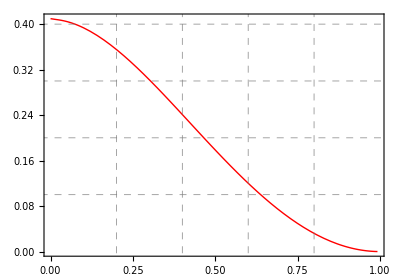

```mathematica
Show[Plot[Evaluate[Atn[r](1-r)^2/.solm],{r,0,ϵh},PlotRange->All,PlotStyle->{Red,Thick}],AspectRatio->0.7,Frame->True,FrameTicksStyle->Directive[Black,18],GridLines->{{0.2,0.4,0.6,0.8},{0.1,0.2,0.3,0.4}},GridLinesStyle->Directive[Gray,Dashed]]
```

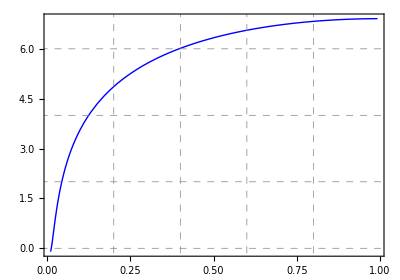

```mathematica
Show[Plot[Evaluate[ϕ[r]/.solm],{r,0.01,ϵh},PlotRange->All,PlotStyle->{Blue,Thick}],AxesOrigin->{0,0},AspectRatio->0.7,Frame->True,FrameTicksStyle->Directive[Black,18],GridLines->{{0.2,0.4,0.6,0.8},{0,2,4,6}},GridLinesStyle->Directive[Gray,Dashed]]
```

The solution at the boundary needs to be rescaled by a parameter, which is given by

```mathematica
ϵb=0.0000001;
λ=Sqrt[(4 r^2)/rp^2(fn[r]G[r])/g[r]^2/.r->ϵb/.solm⟦1⟧]
```

0.0142772

And we can check that we obtain AdS asymptotics, as expected:

```mathematica
(4 r^2)/(λ^2 rp^2)(fn[r]G[r])/g[r]^2/.r->ϵb/.solm
r^2(g'[r]^2 G[r])/(g[r]^2 fn[r])/.r->ϵb/.solm
(4 r^2)/rp^2 1/g[r]^2/.r->ϵb/.solm
```

{1.}

{1.}

{1.}

### γ = -√3, δ = -1/√3 case

This is the choice of coefficients for this section.
ϵ is just there to improve performance.

```mathematica
ϵ=1/1000000;γ0=-√3;δ0=-1/√3+ϵ;B0=100;Q0=1;β0=-3/2;
```

```mathematica
prec=60;
```

#### Bdry conditions

```mathematica
Clear[γ,δ,B,Q,rp]
```

Here we check the result obtained from the attractor equations, and find the BC that we need to impose to our ansatz.
Notice that for the extremal case, the expansion of f[r] starts at the 4th power, like it happened in the RN solution.

```mathematica
fh[r_]:=cf(r-1)^4+O[r,1]^6;Gh[r_]:=cg+O[r,1]^2;Ath[r_]:=ca(r-1)^2+O[r,1]^4;ϕh[r_]:=cϕ+O[r,1]^2;
subs={f->Function[r,fh[r]],G->Function[r,Gh[r]],At->Function[r,Ath[r]],ϕ->Function[r,ϕh[r]]};
```

```mathematica
AdS2xR2cond={cf cg rp^2-cg/cf};
```

We have solutions for v and w. Let’s see if they match what we get from plugging in that expansion into our EOM.

```mathematica
eqsexp0=eqs/.potentialschoice/.subs//FullSimplify
```

{(-2 rp^2 β Cosh[cϕ δ]-((B^2 cg^2+ca^2 rp^2) Sech[cϕ γ])/(8 cg^2 rp^2))+O[r-1]^2,O[r-1]^0,(cf rp^2 (cf+2 cg β Cosh[cϕ δ])-(cf (B^2 cg^2+ca^2 rp^2) Sech[cϕ γ])/(8 cg rp^2)) (r-1)^4+O[r-1]^6,(-8-(16 cg β Cosh[cϕ δ])/cf+((B^2 cg^2+ca^2 rp^2) Sech[cϕ γ])/(cf cg rp^4))/(2 (r-1)^2)+O[r-1]^0,(-4 β δ Sinh[cϕ δ]+((B^2-(ca^2 rp^2)/cg^2) γ Sech[cϕ γ] Tanh[cϕ γ])/(4 rp^4))+O[r-1]^2}

Replacing Cosh, Sinh... by the appropriate exponentials (for large cϕ), and adding an extra condition for having AdS2 x R2 in the IR...

```mathematica
sol0a=FullSimplify[Solve[Join[Normal[eqsexp0],AdS2xR2cond]==0,{ca,cf,cg,B}]]⟦1⟧
```

{ca→-(Sech[cϕ δ] √(-δ Sinh[cϕ δ]-γ Cosh[cϕ δ] Tanh[cϕ γ]))/(√2 √β √γ √Sech[cϕ γ] √Tanh[cϕ γ]),cf→1/rp,cg→-Sech[cϕ δ]/(4 rp β),B→-(2 √2 √(rp^4 β (δ Sinh[cϕ δ]-γ Cosh[cϕ δ] Tanh[cϕ γ])))/(√γ √Sech[cϕ γ] √Tanh[cϕ γ])}

```mathematica
γ=γ0;δ=δ0;B=B0;Q=Q0;β=β0;
rp=((γ B^2)/(2 β(δ-γ)))^(1/4)((Q^2 (γ-δ))/(B^2 (γ+δ)))^((δ+γ)/(8 γ));
```

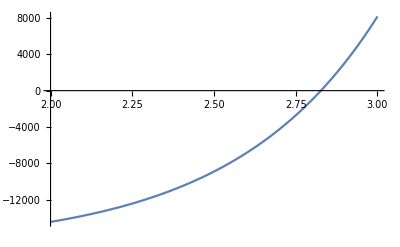

```mathematica
Plot[γ B^2-8 rp^4 β Cosh[cϕ γ] (-γ Cosh[cϕ δ]+δ Coth[cϕ γ] Sinh[cϕ δ]),{cϕ,2,3}]
```

```mathematica
sol0ϕ=FindRoot[γ B^2-8 rp^4 β Cosh[cϕ γ] (-γ Cosh[cϕ δ]+δ Coth[cϕ γ] Sinh[cϕ δ]),{cϕ,2.8},WorkingPrecision->prec];
sol0=N[Join[sol0a⟦1;;3⟧/.sol0ϕ,sol0ϕ],prec];
```

```mathematica
fh[r_]:=cf(r-1)^4+cf1(r-1)^6+O[r,1]^8;Gh[r_]:=cg+cg1(r-1)^2+O[r, 1]^4;Ath[r_]:=ca(r-1)^2+ca1(r-1)^4+O[r, 1]^6;ϕh[r_]:=cϕ+cϕ1(r-1)^2+O[r, 1]^4;
subs={f->Function[r,fh[r]],G->Function[r,Gh[r]],At->Function[r,Ath[r]],ϕ->Function[r,ϕh[r]]};
```

```mathematica
eqsexp1=eqs/.potentialschoice/.subs/.sol0//FullSimplify;
sol1=Chop[Solve[{SeriesCoefficient[eqsexp1⟦1⟧,2],SeriesCoefficient[eqsexp1⟦2⟧,0],SeriesCoefficient[eqsexp1⟦3⟧,6],SeriesCoefficient[eqsexp1⟦4⟧,0],SeriesCoefficient[eqsexp1⟦5⟧,2]}==0,{cf1,cg1,cϕ1}]⟦1⟧,10^-18]
```

{cf1→-0.471394687179665519884179614238621836408771268701464,cg1→-0.21628790080696809160974901358719753327983211604821236+0.02345786116148132018116295719493657440413215453654183 ca1,cϕ1→3.2112547819948173389541924688216363127870689330329064}

```mathematica
fh[r_]:=cf(r-1)^4+cf1(r-1)^6+cf2(r-1)^8+O[r,1]^10;Gh[r_]:=cg+cg1(r-1)^2+cg2(r-1)^4+O[r, 1]^6;Ath[r_]:=ca(r-1)^2+ca1(r-1)^4+ca2(r-1)^6+O[r, 1]^8;ϕh[r_]:=cϕ+cϕ1(r-1)^2+cϕ2(r-1)^4+O[r, 1]^6;
subs={f->Function[r,fh[r]],G->Function[r,Gh[r]],At->Function[r,Ath[r]],ϕ->Function[r,ϕh[r]]};
```

```mathematica
eqsexp2=eqs/.potentialschoice/.subs/.sol0/.sol1//FullSimplify;
eqsexp2b={SeriesCoefficient[eqsexp2⟦1⟧,4],SeriesCoefficient[eqsexp2⟦2⟧,2],SeriesCoefficient[eqsexp2⟦3⟧,8],SeriesCoefficient[eqsexp2⟦4⟧,2],SeriesCoefficient[eqsexp2⟦5⟧,4]};
```

```mathematica
sol11=Solve[eqsexp2b⟦1⟧==0,cϕ2]⟦1⟧//Simplify;coef2=eqsexp2b⟦2⟧/.sol11//Simplify;sol12=Solve[coef2==0,ca1]⟦1⟧//Simplify;sol13=sol11/.sol12//Simplify;coef3=eqsexp2b⟦3⟧/.Join[sol12,sol13]//Simplify;sol14=Solve[coef3==0,cg2]⟦1⟧//Simplify;sol15=sol13/.sol14//Simplify;eqsexp2b⟦4⟧/.Join[sol15,sol14,sol12]//Simplify
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.+0. ca2+0. cf2

```mathematica
coef5=eqsexp2b⟦5⟧/.Join[sol15,sol14,sol12]//Simplify;
sol16=Solve[coef5==0,cf2]⟦1⟧//Simplify;
sol2=Chop[Join[sol16,sol15/.sol16,sol14/.sol16,sol12]//Simplify,10^-18]
```

{cf2→8.81408916298546024089514239275410180866-0.186856667363575766739413351172464761929 ca2,cϕ2→0.70663802661750497933346344031699536509,cg2→-1.2067628979723383744308112626405169355+0.035186791742221980271744435792404861606 ca2,ca1→13.494391280540995565141595053231048968350282}

```mathematica
fh[r_]:=cf(r-1)^4+cf1(r-1)^6+cf2(r-1)^8+cf3(r-1)^10+O[r,1]^12;Gh[r_]:=cg+cg1(r-1)^2+cg2(r-1)^4+cg3(r-1)^6+O[r, 1]^8;Ath[r_]:=ca(r-1)^2+ca1(r-1)^4+ca2(r-1)^6+ca3(r-1)^8+O[r, 1]^10;ϕh[r_]:=cϕ+cϕ1(r-1)^2+cϕ2(r-1)^4+cϕ3(r-1)^6+O[r, 1]^8;
subs={f->Function[r,fh[r]],G->Function[r,Gh[r]],At->Function[r,Ath[r]],ϕ->Function[r,ϕh[r]]};
```

```mathematica
eqsexp3=eqs/.potentialschoice/.subs/.sol0/.sol1/.sol2//FullSimplify;
eqsexp3b={SeriesCoefficient[eqsexp3⟦1⟧,6],SeriesCoefficient[eqsexp3⟦2⟧,4],SeriesCoefficient[eqsexp3⟦3⟧,10],SeriesCoefficient[eqsexp3⟦4⟧,4],SeriesCoefficient[eqsexp3⟦5⟧,6]};
```

```mathematica
sol3=Chop[Solve[eqsexp3b==0]⟦1⟧,10^-18]
```

{ca2→37.79817633639792843126275429042082,cf3→29.2419137267261282225048870645431-0.3737133347271515334788267023449295 ca3,cg3→-3.618189855003181584432570655468833+0.04691572232296264036232591438987315 ca3,cϕ3→-1.791838659492892398053320298051454}

```mathematica
solexp=Join[sol0,sol1/.sol2,sol2/.sol3,sol3];
```

```mathematica
fh[r_]:=cf(r-1)^4+cf1(r-1)^6+cf2(r-1)^8+O[r,1]^10;Gh[r_]:=cg+cg1(r-1)^2+cg2(r-1)^4+O[r, 1]^6;Ath[r_]:=ca(r-1)^2+ca1(r-1)^4+ca2(r-1)^6+O[r, 1]^8;ϕh[r_]:=cϕ+cϕ1(r-1)^2+cϕ2(r-1)^4+O[r, 1]^6;
{fh[r],Gh[r],Ath[r],ϕh[r]}/.solexp
```

{0.619577333351611049976407257391286088761792899783817144117522 (r-1)^4-0.471394687179665519884179614238621836408771268701464 (r-1)^6+1.751247900345371605667418781492835 (r-1)^8+O[r-1]^10,0.038890662210847197696533505408089476386956272656157495021403+0.1002616563106667061818930763913684966077317 (r-1)^2+0.123233661012278517174849749327293 (r-1)^4+O[r-1]^6,3.3157892736365163918271556564791048232894680610745523369928 (r-1)^2+13.494391280540995565141595053231048968350282 (r-1)^4+37.79817633639792843126275429042082 (r-1)^6+O[r-1]^8,2.82698995582478019026765934269711048619209984889327099787304+3.2112547819948173389541924688216363127870689330329064 (r-1)^2+0.70663802661750497933346344031699536509 (r-1)^4+O[r-1]^6}

#### Integration

From the final set of eqs derived above:

```mathematica
eqssimple={ϕ''[r]-(ϕ''[r]/.repl),Atn''[r]-(Atn''[r]/.repl),fn''[r]-(fn''[r]/.repl),G'[r]-(G'[r]/.repl)}//Expand//Simplify;
```

```mathematica
ϵh=1-75/10000;
```

These are the Boundary conditions for this case:

```mathematica
fBC=Evaluate[fh[r]/(r-1)^4/.solexp//Normal]/.r->ϵh
AtBC=Evaluate[Ath[r]/(r-1)^2/.solexp//Normal]/.r->ϵh
ϕBC=Evaluate[ϕh[r]/.solexp//Normal]/.r->ϵh
fpBC=Evaluate[D[fh[r]/(r-1)^4,r]/.solexp//Normal]/.r->ϵh
AtpBC=Evaluate[D[Ath[r]/(r-1)^2,r]/.solexp//Normal]/.r->ϵh
ϕpBC=Evaluate[D[ϕh[r],r]/.solexp//Normal]/.r->ϵh
GBC=Evaluate[Gh[r]/.solexp//Normal]/.r->ϵh
```

0.619550822941515003477441118345052404600667

3.31654845274183913721176529824315756682856

2.8271705911421142798374248646957683698626872689

0.007067965076863149983678130444385558388

-0.20247965363068260498135168169633081965

-0.0481700141815921771239655122518800796214846

0.038896302318933678245418732642184525845778

Now we integrate from the horizon to the boundary

```mathematica
solm=NDSolve[{-1/2 (-2+r)^4 r^4 γ Sech[γ ϕ[r]] Tanh[γ ϕ[r]] (-4 B^2 G[r]^2+rp^2 (2 Atn[r]+(-1+r) Atn'[r])^2)+2 rp^4 G[r] (-16 β δ G[r] Sinh[δ ϕ[r]]+(-2+r) (-1+r) r ((-(4+(-2+r) r) fn[r]+(-2+r) (-1+r) r fn'[r]) ϕ'[r]+(-2+r) (-1+r) r fn[r] ϕ''[r]))==0,2 Atn[r] ϕ'[r] (-8 (-1+r) γ Tanh[γ ϕ[r]]+(-2+r) r ϕ'[r])+(-1+r) Atn'[r] (24-8 (-1+r) γ Tanh[γ ϕ[r]] ϕ'[r]+(-2+r) r ϕ'[r]^2)+8 (-1+r)^2 Atn''[r]==0,-2 (-2+r)^4 (-1+r) r^4 Sech[γ ϕ[r]] (4 B^2 G[r]^2+rp^2 (2 Atn[r]+(-1+r) Atn'[r])^2)-1/2 (-2+r)^5 r^5 γ Sech[γ ϕ[r]] Tanh[γ ϕ[r]] (-4 B^2 G[r]^2+rp^2 (2 Atn[r]+(-1+r) Atn'[r])^2) ϕ'[r]+rp^4 G[r] (32 β G[r] (4 (-1+r) Cosh[δ ϕ[r]]-(-2+r) r δ Sinh[δ ϕ[r]] ϕ'[r])+2 (-1+r) fn[r] (32 (3+2 (-2+r) r)-(-2+r)^2 r^2 (3+(-2+r) r) ϕ'[r]^2)+(-2+r) (-1+r)^2 r (fn'[r] (-8 (8+(-2+r) r)+(-2+r)^2 r^2 ϕ'[r]^2)+8 (-2+r) (-1+r) r fn''[r]))==0,8 (-1+r)G'[r]+(-2+r) r G[r] ϕ'[r]^2==0,fn[ϵh]==fBC,Atn[ϵh]==AtBC,ϕ[ϵh]==ϕBC,fn'[ϵh]==fpBC,Atn'[ϵh]==AtpBC,ϕ'[ϵh]==ϕpBC,G[ϵh]==GBC},{fn,Atn,ϕ,G},{r,ϵh,0},AccuracyGoal->10,PrecisionGoal->10];
```

NDSolve::ndsz: At r == 5.56619×10^-11, step size is effectively zero; singularity or stiff system suspected.

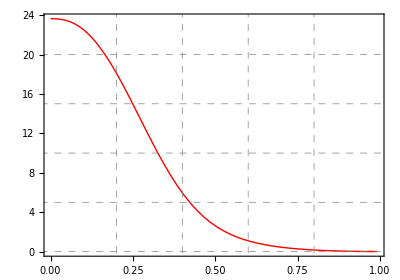

```mathematica
Show[Plot[Evaluate[Atn[r](1-r)^2/.solm],{r,0,ϵh},PlotRange->All,PlotStyle->{Red,Thick}],AspectRatio->0.7,Frame->True,FrameTicksStyle->Directive[Black,18],GridLines->{{0.2,0.4,0.6,0.8},{0,5,10,15,20}},GridLinesStyle->Directive[Gray,Dashed]]
```

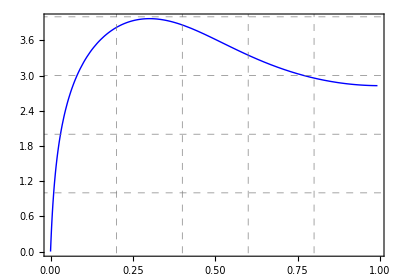

```mathematica
Show[Plot[Evaluate[ϕ[r]/.solm],{r,0,ϵh},PlotRange->All,PlotStyle->{Blue,Thick}],AxesOrigin->{0,0},AspectRatio->0.7,Frame->True,FrameTicksStyle->Directive[Black,18],GridLines->{{0.2,0.4,0.6,0.8},{1,2,3,4}},GridLinesStyle->Directive[Gray,Dashed]]
```

Curvature check:

```mathematica
plotricci=Plot[Evaluate[1/(4 (-1+r)^3 G[r]^3)(-(-2+r) r G[r] (r (2-3 r+r^2) f'[r] G'[r]+G[r] ((-12+26 r-13 r^2) f'[r]+r (2-3 r+r^2) f''[r]))+f[r] (-48 (-1+r)^3 G[r]^2+(-2+r)^2 (-1+r) r^2 G'[r]^2+(-2+r)^2 r^2 G[r] (G'[r]-(-1+r) G''[r])))/.f->Function[r,fn[r](r-1)^4]/.solm],{r,0,ϵh},PlotRange->All,PlotStyle->{Darker[Green],Thick}];
```

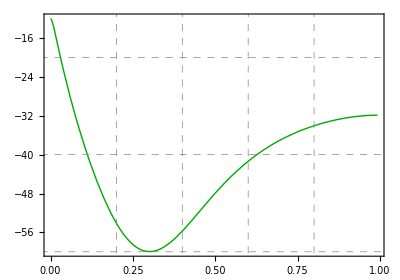

```mathematica
Show[plotricci,AspectRatio->0.7,Frame->True,FrameTicksStyle->Directive[Black,18],GridLines->{{0.2,0.4,0.6,0.8},{-60,-40,-20,0}},AxesOrigin->{0,0},GridLinesStyle->Directive[Gray,Dashed]]
```

The solution at the boundary needs to be rescaled by a parameter, which is given by

```mathematica
ϵb=0.0000001;
λ=Sqrt[(4 r^2)/rp^2(fn[r]G[r])/g[r]^2/.r->ϵb/.solm⟦1⟧]
```

0.169184

And we can check that we obtain AdS asymptotics, as expected:

```mathematica
(4 r^2)/(λ^2 rp^2)(fn[r]G[r])/g[r]^2/.r->ϵb/.solm
r^2(g'[r]^2 G[r])/(g[r]^2 fn[r])/.r->ϵb/.solm
(4 r^2)/rp^2 1/g[r]^2/.r->ϵb/.solm
```

{1.}

{1.}

{1.}

#### EOM checking

A few numerical checks

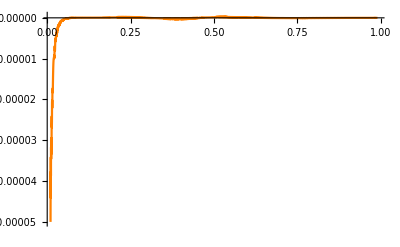

```mathematica
Plot[Evaluate[constr[[1]]/.potentialschoice/.solm],{r,0.01,0.99},PlotRange->All,PlotStyle->{Orange}]
```

```mathematica
Plot[Evaluate[eqsn[[1]]/.potentialschoice/.solm],{r,0.01,0.99},PlotRange->All,PlotStyle->{Orange}]
```

-Graphics-

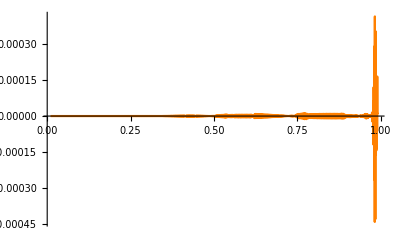

```mathematica
Plot[Evaluate[eqsn[[2]]/.potentialschoice/.solm],{r,0.01,0.99},PlotRange->All,PlotStyle->{Orange}]
```

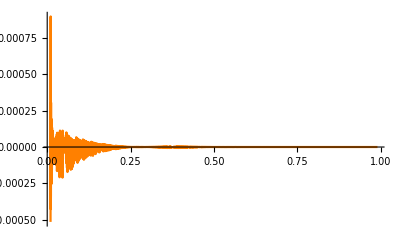

```mathematica
Plot[Evaluate[eqsn[[3]]/.potentialschoice/.solm],{r,0.01,0.99},PlotRange->All,PlotStyle->{Orange}]
```

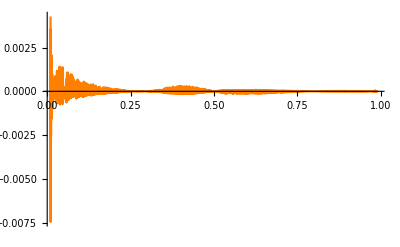

```mathematica
Plot[Evaluate[fn[r]eqsn[[4]]/.potentialschoice/.solm],{r,0.01,0.99},PlotRange->All,PlotStyle->{Orange}]
```

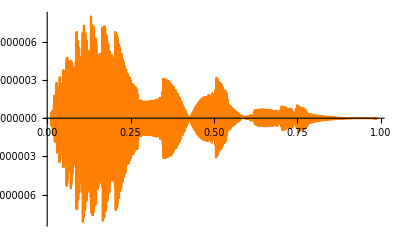

```mathematica
Plot[Evaluate[eqsn[[5]]/.potentialschoice/.solm],{r,0.01,0.99},PlotRange->All,PlotStyle->{Orange}]
```

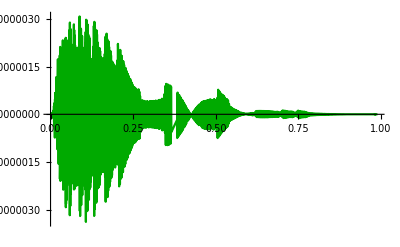

```mathematica
PlotEOM1=Plot[Evaluate[-1/2 (-2+r)^4 r^4 γ Sech[γ ϕ[r]] Tanh[γ ϕ[r]] (-4 B^2 G[r]^2+rp^2 (2 Atn[r]+(-1+r) Atn'[r])^2)+2 rp^4 G[r] (-16 β δ G[r] Sinh[δ ϕ[r]]+(-2+r) (-1+r) r ((-(4+(-2+r) r) fn[r]+(-2+r) (-1+r) r fn'[r]) ϕ'[r]+(-2+r) (-1+r) r fn[r] ϕ''[r]))/.solm],{r,0,0.99},PlotRange->All,PlotStyle->{Darker[Green]}]
```

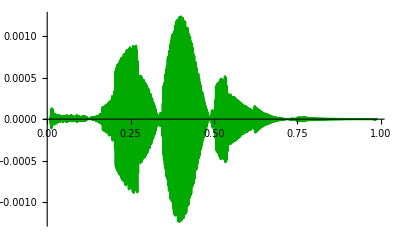

```mathematica
PlotEOM2=Plot[Evaluate[2 Atn[r] ϕ'[r] (-8 (-1+r) γ Tanh[γ ϕ[r]]+(-2+r) r ϕ'[r])+(-1+r) Atn'[r] (24-8 (-1+r) γ Tanh[γ ϕ[r]] ϕ'[r]+(-2+r) r ϕ'[r]^2)+8 (-1+r)^2 Atn''[r]/.solm],{r,0.01,0.99},PlotRange->All,PlotStyle->{Darker[Green]}]
```

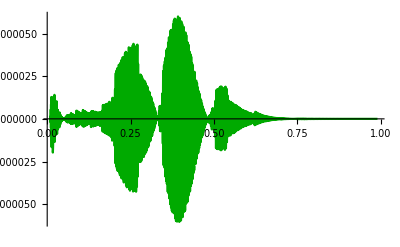

```mathematica
PlotEOM3=Plot[Evaluate[-2 (-2+r)^4 (-1+r) r^4 Sech[γ ϕ[r]] (4 B^2 G[r]^2+rp^2 (2 Atn[r]+(-1+r) Atn'[r])^2)-1/2 (-2+r)^5 r^5 γ Sech[γ ϕ[r]] Tanh[γ ϕ[r]] (-4 B^2 G[r]^2+rp^2 (2 Atn[r]+(-1+r) Atn'[r])^2) ϕ'[r]+rp^4 G[r] (32 β G[r] (4 (-1+r) Cosh[δ ϕ[r]]-(-2+r) r δ Sinh[δ ϕ[r]] ϕ'[r])+2 (-1+r) fn[r] (32 (3+2 (-2+r) r)-(-2+r)^2 r^2 (3+(-2+r) r) ϕ'[r]^2)+(-2+r) (-1+r)^2 r (fn'[r] (-8 (8+(-2+r) r)+(-2+r)^2 r^2 ϕ'[r]^2)+8 (-2+r) (-1+r) r fn''[r]))/.solm],{r,0.01,0.99},PlotRange->All,PlotStyle->{Darker[Green]}]
```

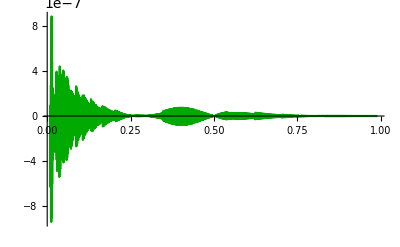

```mathematica
PlotEOM3=Plot[Evaluate[8 (-1+r)G'[r]+(-2+r) r G[r] ϕ'[r]^2/.solm],{r,0.01,0.99},PlotRange->All,PlotStyle->{Darker[Green]}]
```